Curtis Sera
v 1.0
2019-08-08

Let’s make our piecewise function for the protrusion membrane surface and graph it as a surface of revolution:

Piecewise[{{700-200 √(1-(200-z)^2/40000), 0<z≤200}, {500, 200<z≤4500}, {500 √(1-(-4500+z)^2/250000), 4500<z≤5000}, {0, True}}]

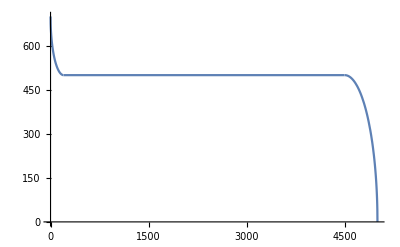

-Graphics3D-

```mathematica
R = 500; (*Dist b/w membrane and z axis*)
rt = 200; (*Radius of the torus tube for the base*)
l = 5000; (*Protrusion length*)

rl[z_] := R+rt-rt Cos[ArcSin[(rt-z)/rt]];(*local radius of curvature for toroidal base*)

pwR = Piecewise[{{rl[z],0<z≤rt},
{R,rt<z≤l-R},
{(z-(l-R)) Tan[ArcCos[(z-(l-R))/R]],l-R<z≤ l}}]
Plot[pwR,{z,0,l}]
RevolutionPlot3D[{pwR,z},{z,0,l}] 
	(*Note how we put pwR as "x" and put z last to make it the axis of revolution*)
```

Great!
Now ideally I’d just import the tension data already computed via MATLAB, but I can’t seem to figure out how to use said data to make a color map :\
Instead, we’ll basically just recompute all of that...

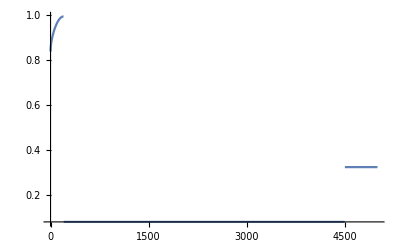

```mathematica
Kbend = 15;

pwTensionNormd[z_]:= Piecewise[{{Kbend*0.5*(((1/rt)+(1/rl[z]))^2)/0.00037,0<z≤rt},
{Kbend*0.5/(R^2)/0.00037,rt<z≤l-R},
{Kbend*2/(R^2)/0.00037,l-R<z≤ l}}]

Plot[pwTensionNormd[z],{z,0,l}]
```

Note: we had to divide each portion by 0.00038 (roughly the max tension) as a hacky, hard-coded way to normalize the values. Couldn’t figure out how to get the max of a piecewise function...
Next, we' ll re - graph our surface using above piecewise function as the coloring guide

```mathematica
tension3dPlot=RevolutionPlot3D[{pwR,z},{z,0,l},
ColorFunction->Function[{x,y,z},
Hue[2(1-pwTensionNormd[z])/3]],ColorFunctionScaling->False]
```

-Graphics3D-

Notes on Hue[]: 
- To make red correspond to the highest tension, we’ve inverted the scale via 1-pwTension[z]
- To fix the default scheme’s color weirdness (they have magenta/violet as the min which looks a lot like the max’s red), we’ve done 2/3 to basically cut out the magenta